# Setup

```mathematica
SetDirectory[NotebookDirectory[]];
Get["C:\\Users\\Miguel\\Github\\Entropy\\Long time mean\\QMB_offline.wl"];
```

```mathematica
Needs["MaTeX`"]
```

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

# Mean with h

```mathematica
Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
Clear[sdiag];
sdiag[L_,La_,Lb_,ini_]:=Module[{state=Dyad[ini],dima=2^(L-La),dimb=2^(L-Lb),rho},
rho=MatrixPartialTrace[state,1,{dima,dimb}];
Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]
];
Clear[svn];
svn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,t_]:=Module[{state=StateEvolution[t,ini,eigenval,eigenvec],rho,λ,purity,dima=2^(L-La),dimb=2^(L-Lb),vn},
rho=MatrixPartialTrace[Dyad[state],1,{dima,dimb}];
Chop[Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]]
];
```

```mathematica
L=8;
g=J=1;
h=0.1;
H=IsingNNOpenHamiltonian[h,g,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
ipreigenvec=ParallelTable[Total[Abs[i]^4],{i,eigenvec}];
```

```mathematica
La=4;
Lb=L-La;
diagentro=ParallelTable[Chop[sdiag[L,La,Lb,i]],{i,eigenvec}];
```

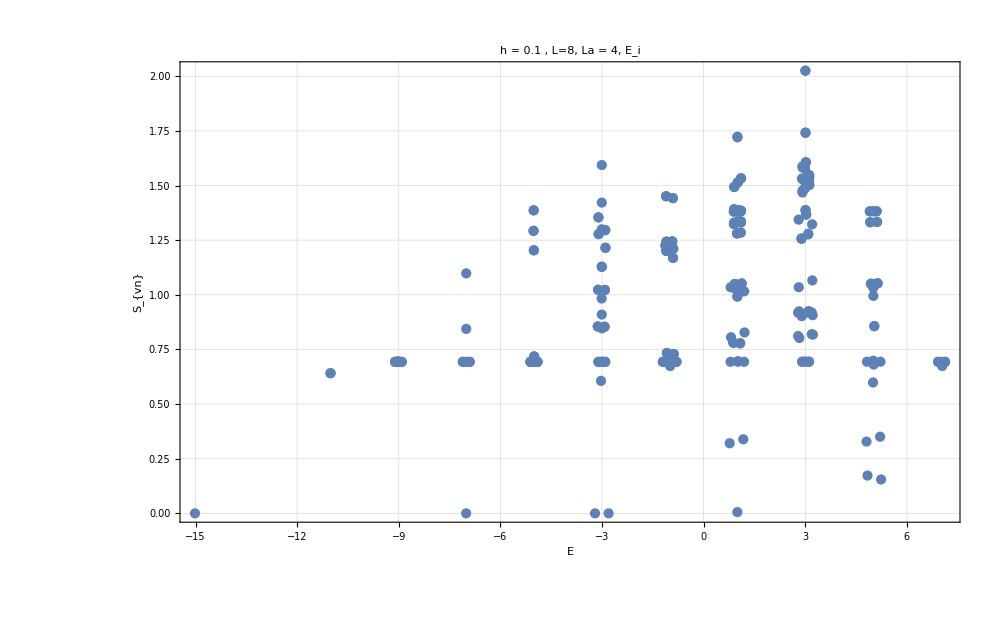

```mathematica
ListPlot[Transpose[{eigenval,diagentro}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["h = "<>ToString[h]<>" , L="<>ToString[L]<>", La = "<>ToString[La]<>", E_i",35,Black],FrameLabel->{Style["E",35,Black],Style["S_{vn}",35,Black]},FrameStyle->Directive[Black,20],ImageSize->1000]
```

```mathematica
tlist=Table[10^i,{i,-1,10,0.0020}];
tlist//Length
```

5501

```mathematica
Clear[haar];
haar[L_Integer]:=Normalize[Table[RandomVariate[NormalDistribution[]]+I RandomVariate[NormalDistribution[]],{2^L}]];
```

```mathematica
productstate2=Table[RandomChainProductState[L],1000];
(*productstate=Table[haar[L],50];*)
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[eigenvec].i]^4]],{i,productstate2},DistributedContexts->Full];
energies=ParallelTable[Chop[Conjugate[i].H.i],{i,productstate2},DistributedContexts->Full];
```

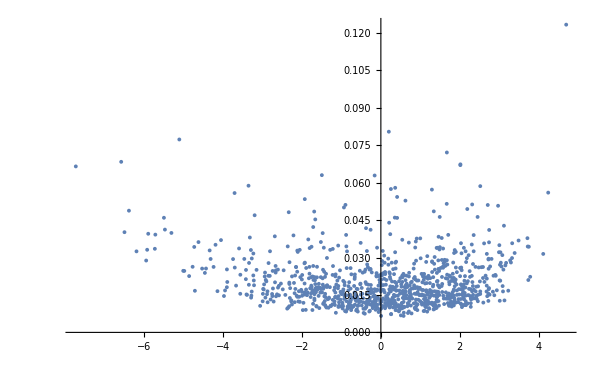

```mathematica
ListPlot[Transpose[{energies,iprs}],PlotRange->All,ImageSize->600]
```

```mathematica
Max[iprs]
Min[iprs]
```

0.123349

0.00660454

```mathematica
threshold=0.0090;
indexs=Flatten[Position[iprs,x_/;x<threshold]];
productstate=Table[productstate2[[i]],{i,indexs}];
productstate//Dimensions
```

{29,256}

```mathematica
threshold=0.05;
indexs=Flatten[Position[iprs,x_/;x>threshold]];
productstate=Table[productstate2[[i]],{i,indexs}];
productstate//Dimensions
```

{26,256}

```mathematica
svntproduct=Table[ParallelTable[{t,svn[L,La,Lb,i,eigenval,eigenvec,t]},{t,tlist},DistributedContexts->Full],{i,productstate}];
```

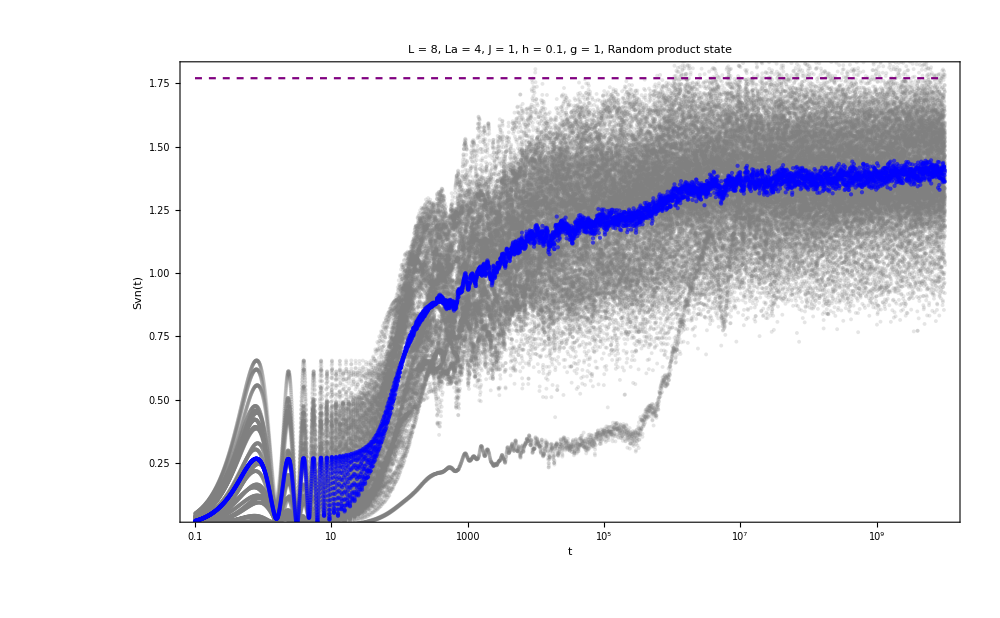

```mathematica
svnplots=ListLogLinearPlot[svntproduct,PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Random product state",20,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotLegends->Automatic,PlotStyle->{Directive[Gray,Opacity[0.2]]}];
svnplotmean=ListLogLinearPlot[Mean[svntproduct],PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Random product state",20,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotLegends->Automatic,PlotStyle->{Directive[Blue,Opacity[0.6],PointSize[0.003]]}];
productstatessvnplot=Show[{svnplots,svnplotmean,LogLinearPlot[Mean[diagentropies],{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Purple,Dashed]]},PlotRange->{All,{0.05,1.8}}]
```

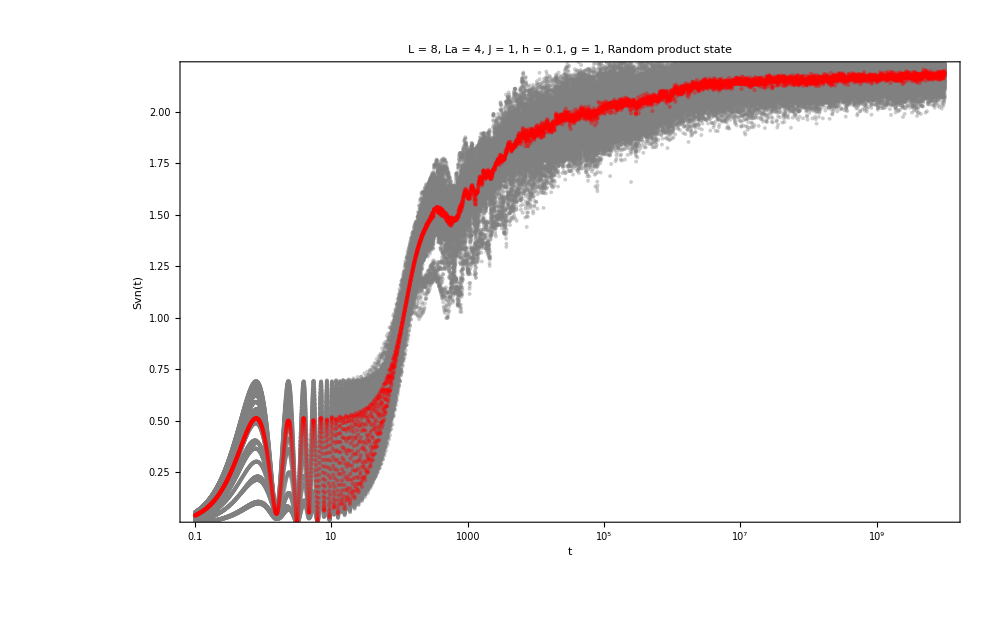

```mathematica
svnplots=ListLogLinearPlot[svntproduct,PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Random product state",20,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotLegends->Automatic,PlotStyle->{Directive[Gray,Opacity[0.4]]}];
svnplotmean=ListLogLinearPlot[Mean[svntproduct],PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Random product state",20,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotLegends->Automatic,PlotStyle->{Directive[Red,Opacity[0.4],PointSize[0.003]]}];
productstatessvnplot=Show[{svnplots,svnplotmean,LogLinearPlot[Mean[diagentropies],{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Orange,Dashed]]},PlotRange->{All,{0.05,2.2}}]
```

```mathematica
newenergies=Table[energies[[i]],{i,indexs}];
newiprs=Table[iprs[[i]],{i,indexs}];
```

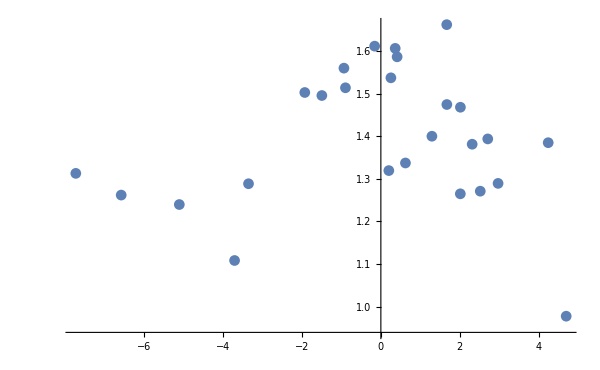

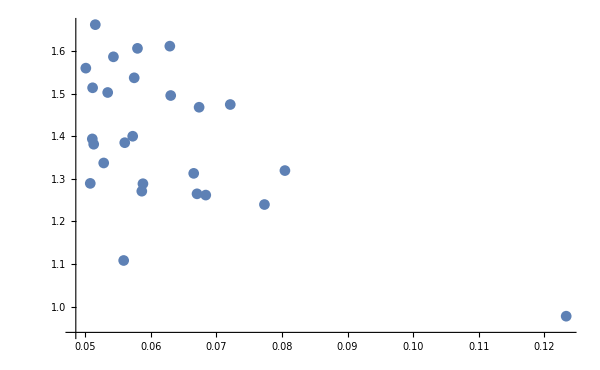

```mathematica
longmean=Table[Mean[svntproduct[[i]][[All,2]][[-500;;-1]]],{i,Length[productstate]}];
ListPlot[Transpose[{newenergies,longmean}],PlotRange->All,ImageSize->600]
ListPlot[Transpose[{newiprs,longmean}],PlotRange->All,ImageSize->600]
```

```mathematica
diagentropies=ParallelTable[sdiag[L,La,Lb,Conjugate[eigenvec].i],{i,productstate},DistributedContexts->Full];
alldata=Sort[Transpose[{newiprs,newenergies,diagentropies,longmean}],First];
```

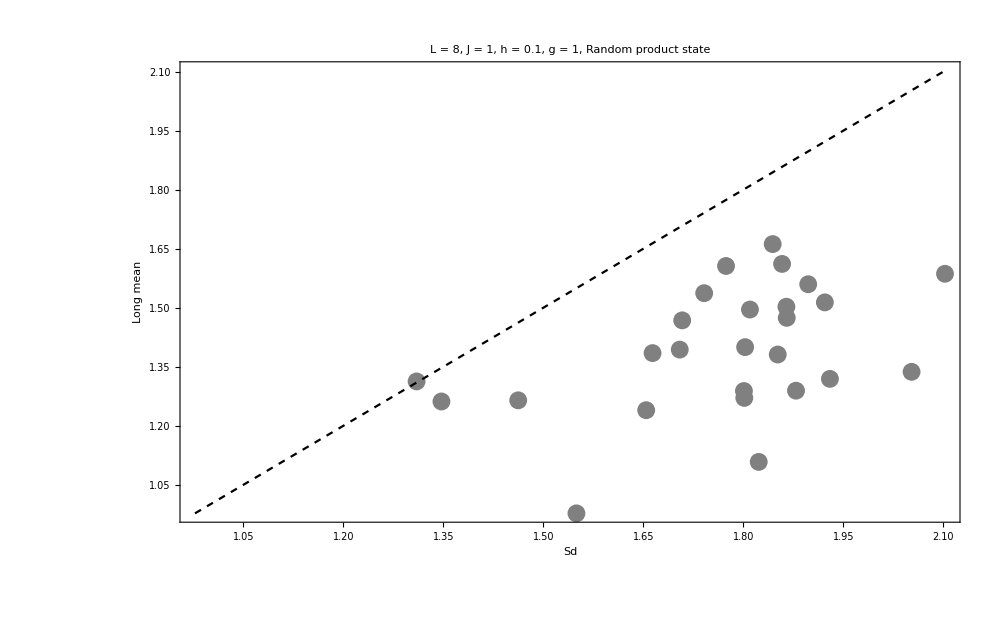

```mathematica
Show[{ListPlot[Transpose[{alldata[[All,3]],alldata[[All,4]]}],PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Random product state",20,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["Sd"],Style["Long mean"]},PlotRange->All,ImageSize->1000,PlotLegends->Automatic,PlotStyle->{Directive[Gray,Opacity[1]]}],Plot[x,{x,Min[Transpose[{alldata[[All,3]],alldata[[All,4]]}]],Max[Transpose[{alldata[[All,3]],alldata[[All,4]]}]]},PlotStyle->Directive[Black,Dashed]]},PlotRange->All]
```

# Mean with J

```mathematica
Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
Clear[sdiag];
sdiag[L_,La_,Lb_,ini_]:=Module[{state=Dyad[ini],dima=2^(L-La),dimb=2^(L-Lb),rho},
rho=MatrixPartialTrace[state,1,{dima,dimb}];
Chop[Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]]
];
Clear[svn];
svn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,t_]:=Module[{state=StateEvolution[t,ini,eigenval,eigenvec],rho,λ,purity,dima=2^(L-La),dimb=2^(L-Lb),vn},
rho=MatrixPartialTrace[Dyad[state],1,{dima,dimb}];
Chop[Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]]
];
```

```mathematica
L=8;
g=1;
J=0.1;
h=1;
H=IsingNNOpenHamiltonian[h,g,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
ipreigenvec=ParallelTable[Total[Abs[i]^4],{i,eigenvec}];
```

```mathematica
La=4;
Lb=L-La;
diagentro=ParallelTable[Chop[sdiag[L,La,Lb,i]],{i,eigenvec}];
```

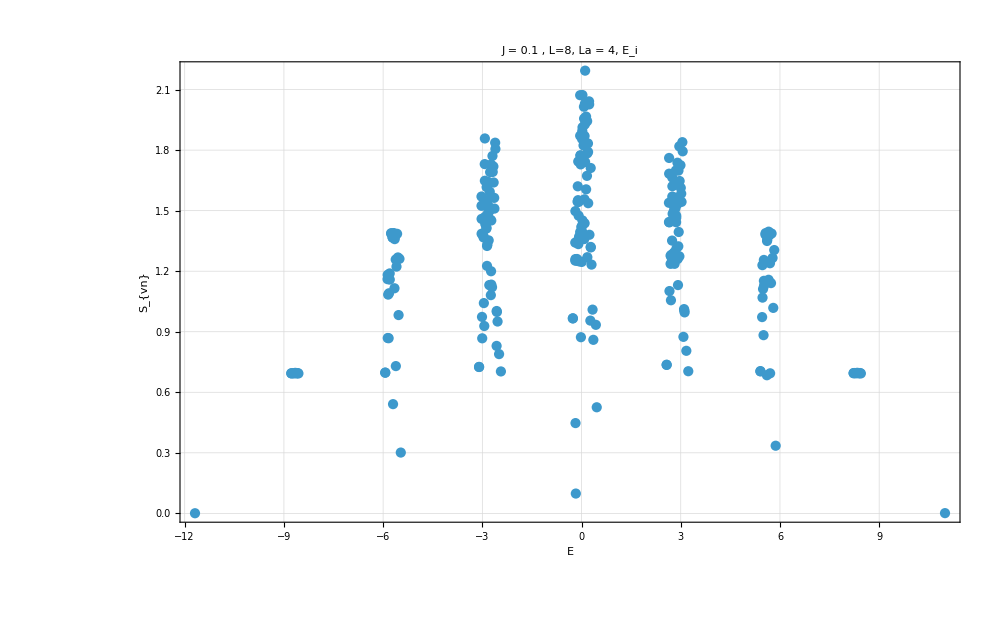

eigenvectors_open_L_8_La_4_J_0.1_h_1.png

```mathematica
plot=ListPlot[Transpose[{eigenval,diagentro}],PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["J = "<>ToString[J]<>" , L="<>ToString[L]<>", La = "<>ToString[La]<>", E_i",35,Black],FrameLabel->{Style["E",35,Black],Style["S_{vn}",35,Black]},FrameStyle->Directive[Black,20],ImageSize->1000]
Export["eigenvectors_open_L_"<>ToString[L]<>"_La_"<>ToString[La]<>"_J_"<>ToString[J]<>"_h_"<>ToString[h]<>".png",plot,ImageResolution->300]
```

```mathematica
tlist=Table[10^i,{i,-1,10,0.0020}];
tlist//Length
```

5501

```mathematica
Clear[haar];
haar[L_Integer]:=Normalize[Table[RandomVariate[NormalDistribution[]]+I RandomVariate[NormalDistribution[]],{2^L}]];
```

```mathematica
productstate2=Table[RandomChainProductState[L],1000];
(*productstate2=Table[haar[L],10];*)
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[eigenvec].i]^4]],{i,productstate2},DistributedContexts->Full];
energies=ParallelTable[Chop[Conjugate[i].H.i],{i,productstate2},DistributedContexts->Full];
```

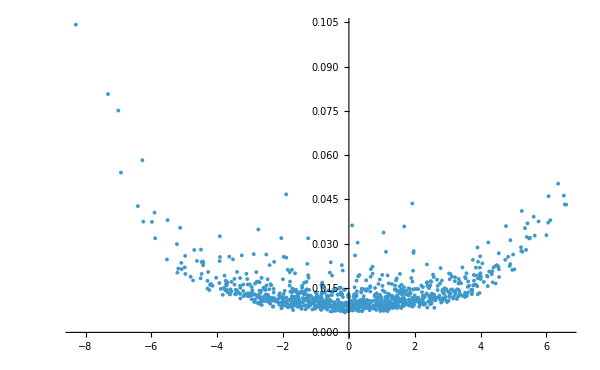

```mathematica
ListPlot[Transpose[{energies,iprs}],PlotRange->All,ImageSize->600]
```

```mathematica
Max[iprs]
Min[iprs]
```

0.104181

0.00676996

```mathematica
(*HIGH IPR*)
threshold=0.030;
indexs=Flatten[Position[iprs,x_/;x>threshold]];
productstate=Table[productstate2[[i]],{i,indexs}];
productstate//Dimensions
```

```mathematica
(*RED*)
threshold=0.0078;
indexs=Flatten[Position[iprs,x_/;x<threshold]];
productstate=Table[productstate2[[i]],{i,indexs}];
productstate//Dimensions
```

{34,256}

```mathematica
indexs=Range[Length[productstate2]];
productstate=productstate2;
svntproduct=Table[ParallelTable[{t,svn[L,La,Lb,i,eigenval,eigenvec,t]},{t,tlist},DistributedContexts->Full],{i,productstate}];
```

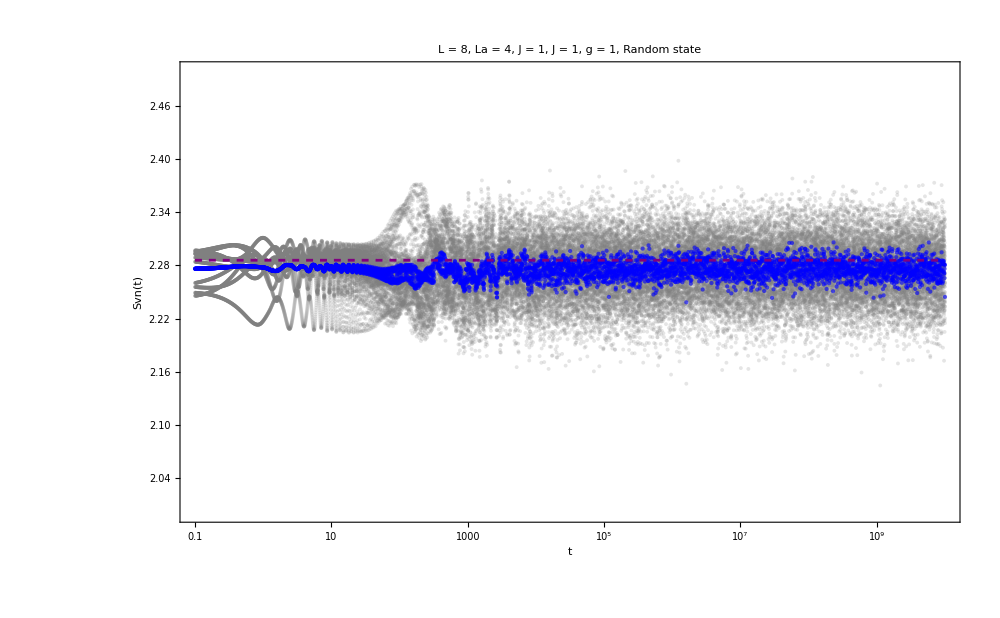

```mathematica
svnplots=ListLogLinearPlot[svntproduct,PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", J = "<>ToString[J]<>", g = "<>ToString[g]<>", Random state",20,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotLegends->Automatic,PlotStyle->{Directive[Gray,Opacity[0.2]]}];
svnplotmean=ListLogLinearPlot[Mean[svntproduct],PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", J = "<>ToString[J]<>", g = "<>ToString[g]<>", Random state",20,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotLegends->Automatic,PlotStyle->{Directive[Blue,Opacity[0.6],PointSize[0.003]]}];
productstatessvnplot=Show[{svnplots,svnplotmean,LogLinearPlot[Mean[diagentropies],{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Purple,Dashed]]},PlotRange->{All,{2,2.5}}]
```

```mathematica
svntproduct=Table[ParallelTable[{t,svn[L,La,Lb,i,eigenval,eigenvec,t]},{t,tlist},DistributedContexts->Full],{i,productstate}];
```

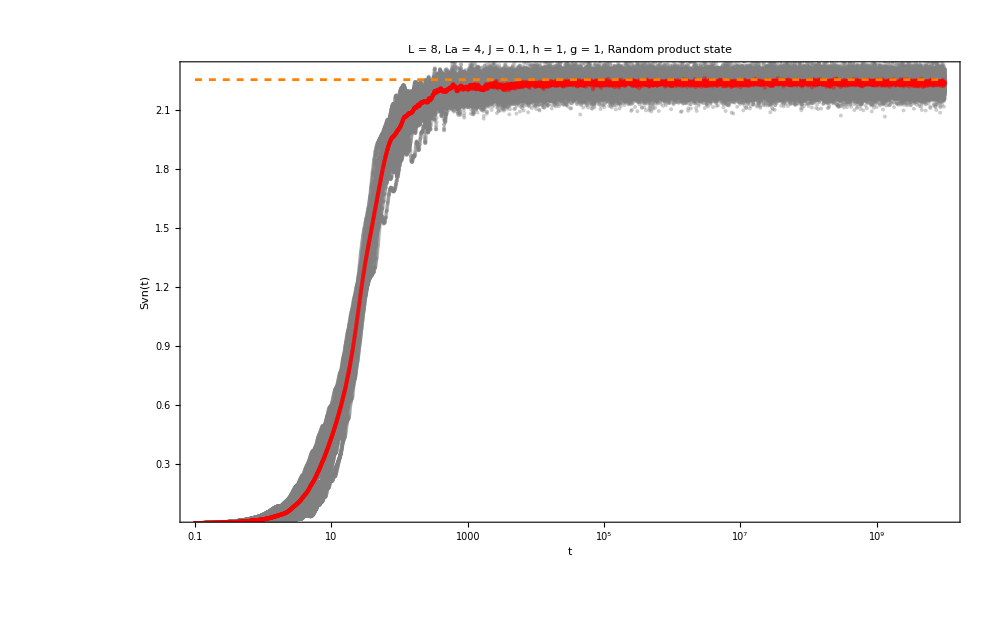

svn_open_randomproductstates_34_L_8_La_4_J_0.1_h_1.png

```mathematica
svnplots=ListLogLinearPlot[svntproduct,PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Random product state",20,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotLegends->Automatic,PlotStyle->{Directive[Gray,Opacity[0.4]]}];
svnplotmean=ListLogLinearPlot[Mean[svntproduct],PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Random product state",20,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotLegends->Automatic,PlotStyle->{Directive[Red,Opacity[0.4],PointSize[0.003]]}];
plot=Show[{svnplots,svnplotmean,LogLinearPlot[Mean[diagentropies],{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Orange,Dashed]]},PlotRange->{All,{0.05,2.3}}]
Export["svn_open_randomproductstates_"<>ToString[Length[productstate]]<>"_L_"<>ToString[L]<>"_La_"<>ToString[La]<>"_J_"<>ToString[J]<>"_h_"<>ToString[h]<>".png",plot,ImageResolution->300]
```

```mathematica
newenergies=Table[energies[[i]],{i,indexs}];
newiprs=Table[iprs[[i]],{i,indexs}];
longmean=Table[Mean[svntproduct[[i]][[All,2]][[-500;;-1]]],{i,Length[productstate]}];
diagentropies=ParallelTable[sdiag[L,La,Lb,Conjugate[eigenvec].i],{i,productstate},DistributedContexts->Full];
alldata=Sort[Transpose[{newiprs,newenergies,diagentropies,longmean}],First];
```

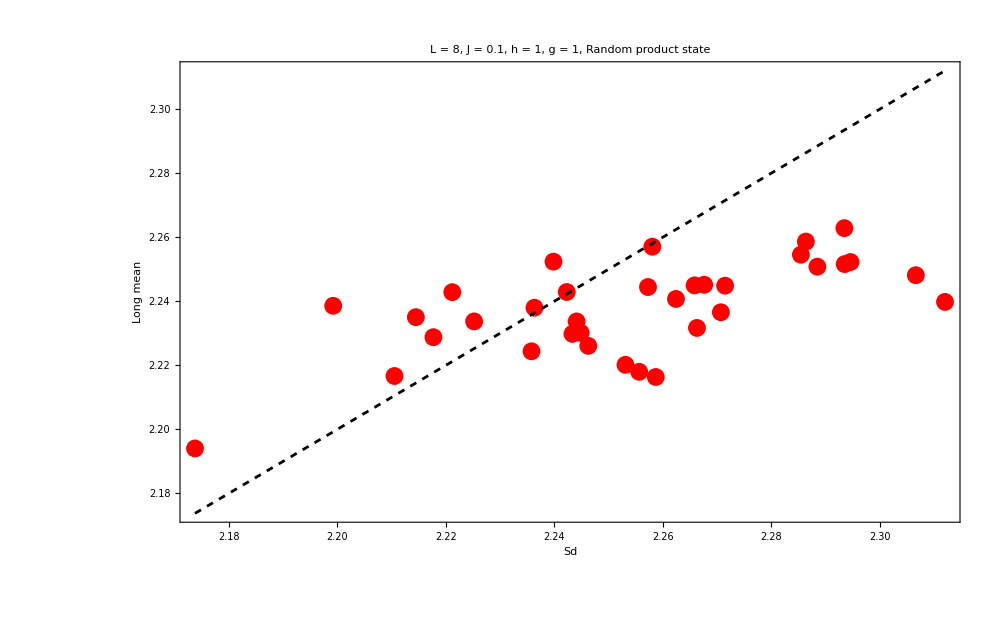

longmean_vs_Sd_open_randomproductstates_34_L_8_La_4_J_0.1_h_1.png

```mathematica
plot=Show[{ListPlot[Transpose[{alldata[[All,3]],alldata[[All,4]]}],PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Random product state",20,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["Sd"],Style["Long mean"]},PlotRange->All,ImageSize->1000,PlotLegends->Automatic,PlotStyle->{Directive[Red,Opacity[1]]}],Plot[x,{x,Min[Transpose[{alldata[[All,3]],alldata[[All,4]]}]],Max[Transpose[{alldata[[All,3]],alldata[[All,4]]}]]},PlotStyle->Directive[Black,Dashed]]},PlotRange->All]
Export["longmean_vs_Sd_open_randomproductstates_"<>ToString[Length[productstate]]<>"_L_"<>ToString[L]<>"_La_"<>ToString[La]<>"_J_"<>ToString[J]<>"_h_"<>ToString[h]<>".png",plot,ImageResolution->300]
```

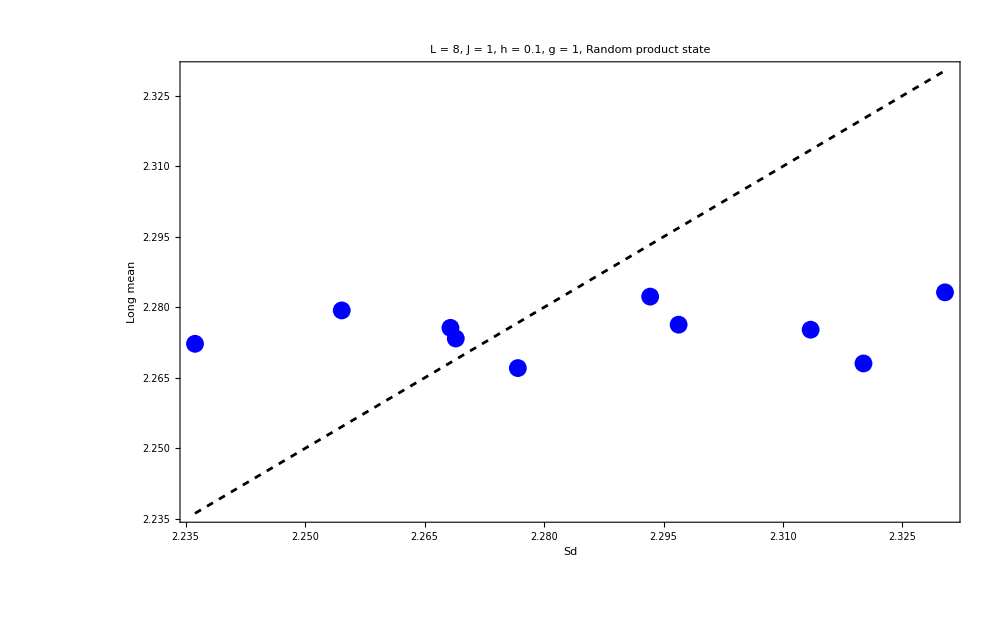

```mathematica
Show[{ListPlot[Transpose[{alldata[[All,3]],alldata[[All,4]]}],PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Random product state",20,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["Sd"],Style["Long mean"]},PlotRange->All,ImageSize->1000,PlotLegends->Automatic,PlotStyle->{Directive[Blue,Opacity[1]]}],Plot[x,{x,Min[Transpose[{alldata[[All,3]],alldata[[All,4]]}]],Max[Transpose[{alldata[[All,3]],alldata[[All,4]]}]]},PlotStyle->Directive[Black,Dashed]]},PlotRange->All]
```

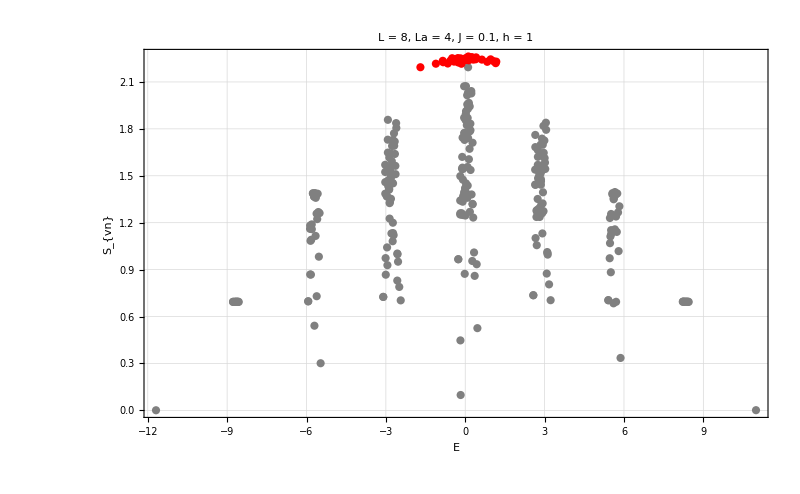

scatter_open_L_8_La_4_J_0.1_h_1.png

```mathematica
plot=ListPlot[{Transpose[{eigenval,diagentro}],Transpose[{newenergies,alldata[[All,4]]}]},PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[h],35,Black],FrameLabel->{Style["E",35,Black],Style["S_{vn}",35,Black]},FrameStyle->Directive[Black,20],ImageSize->800,PlotStyle->{Directive[Gray],Directive[Red]},PlotRange->All]
Export["scatter_open_L_"<>ToString[L]<>"_La_"<>ToString[La]<>"_J_"<>ToString[J]<>"_h_"<>ToString[h]<>".png",plot,ImageResolution->300]
```

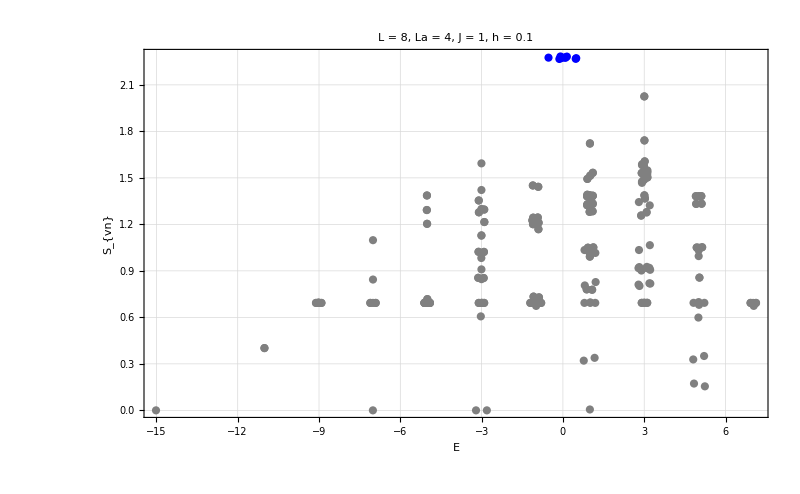

```mathematica
plot=ListPlot[{Transpose[{eigenval,diagentro}],Transpose[{newenergies,alldata[[All,4]]}]},PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[h],35,Black],FrameLabel->{Style["E",35,Black],Style["S_{vn}",35,Black]},FrameStyle->Directive[Black,20],ImageSize->800,PlotStyle->{Directive[Gray],Directive[Blue]},PlotRange->All]
(*Export["scatter_open_L_"<>ToString[L]<>"_La_"<>ToString[La]<>"_J_"<>ToString[J]<>"_h_"<>ToString[h]<>".png",plot,ImageResolution->300]*)
```

## Reduced density matrix

```mathematica
inistate=productstate[[1]];
```

```mathematica
t=10^10;
inistatet=StateEvolution[t,inistate,eigenval,eigenvec];
```

```mathematica
rho=Dyad[inistatet];
```

```mathematica
dima=2^(L-La);
dimb=2^(L-Lb);
```

```mathematica
reducedrho=MatrixPartialTrace[rho,1,{dima,dimb}];
```

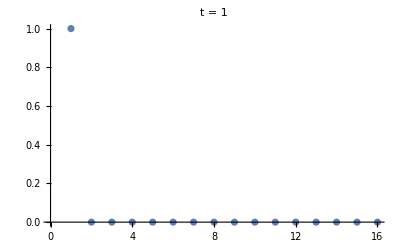

```mathematica
ListPlot[Chop[Eigenvalues[reducedrho]],PlotLabel->Style["t = "<>ToString[t],20,Black]]
```

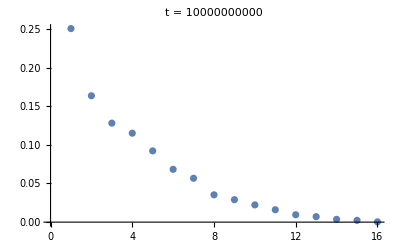

```mathematica
ListPlot[Chop[Eigenvalues[reducedrho]],PlotLabel->Style["t = "<>ToString[t],20,Black]]
```

```mathematica
MatrixPlot[Abs[reducedrho],PlotRange->All,PlotTheme->"Detailed"]
```

-Graphics-

```mathematica
reducedrho//Dimensions
```

{16,16}

```mathematica
diagonal=Table[Chop[reducedrho[[i,i]]],{i,dima}];
diagonal//Sort
```

{0.0310881,0.0388883,0.0483773,0.0537387,0.0571823,0.0585665,0.0586521,0.0619377,0.063058,0.0644044,0.0678584,0.076449,0.0773803,0.0776285,0.0820517,0.0827386}

```mathematica
Total[diagonal]
```

1.

```mathematica
Total[Map[VNentropy,Sort[Chop[Eigenvalues[DiagonalMatrix[diagonal]]]]]]
```

2.74406

```mathematica
Chop[Eigenvalues[reducedrho]]//Sort
```

{0.000351396,0.00230704,0.00359503,0.00705331,0.00955242,0.0160346,0.0222919,0.0290422,0.0353442,0.0567609,0.0683216,0.0922043,0.115075,0.128087,0.163522,0.250457}

```mathematica
Total[Map[VNentropy,Sort[Chop[Eigenvalues[reducedrho]]]]]
```

2.20926